## All of the following is for a Maxwellian

```mathematica
nFac[phiBar_,RB_]:=1/2(Exp[phiBar] Erfc[√phiBar]+2 √((RB-1)/π)DawsonF[√(phiBar/(RB-1))])
```

```mathematica
nFacRBInf[phiBar_]:=1/2(Exp[phiBar] Erfc[√phiBar])+√(phiBar/π)
```

```mathematica
(*Limit[nFac[phiBar,RB],RB->∞,Assumptions->phiBar>0]*)
(*1/2 ((2 √phiBar)/(√π)+ⅇ^phiBar Erfc[√phiBar])*)
```

```mathematica
dPhi=941;T=110;
```

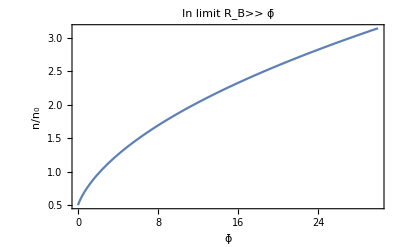

```mathematica
Plot[nFacRBInf[phiBar],{phiBar,0,30},PlotLabel->"In limit R_B>> ϕ̄",Frame->True,FrameLabel->{"ϕ̄","n/n_0"},FrameStyle->(FontSize->18)]
```

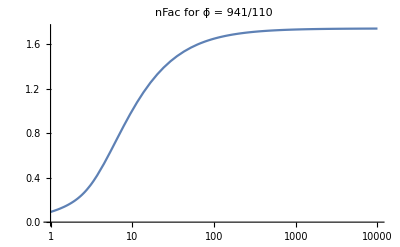

```mathematica
LogLinearPlot[nFac[dPhi/T,RB],{RB,1,10000},PlotLabel->"nFac for ϕ̄ = 941/110"]
```

```mathematica
dPhi=110;T=110;
```

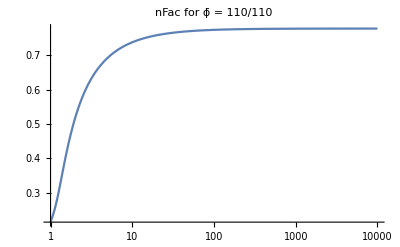

```mathematica
LogLinearPlot[nFac[dPhi/T,RB],{RB,1,10000},PlotLabel->StringForm["nFac for ϕ̄ = `1`/`2`",dPhi,T],PlotRange->All]
```

```mathematica
dPhi=10000;T=110;
```

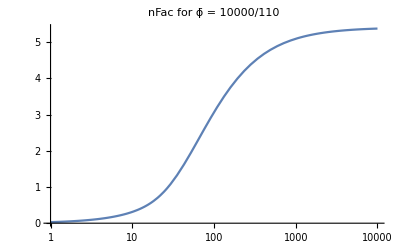

```mathematica
LogLinearPlot[nFac[dPhi/T,RB],{RB,1,10000},PlotLabel->StringForm["nFac for ϕ̄ = `1`/`2`",dPhi,T],PlotRange->All]
```